# Two-Body Central Force Problems

## Juan Jose Neri

### Problem 8.25

Consider a particle with mass m and angular momentum  l in the field of a central force F=-(k*r^(2/5)). To simplify your equations, choose units for which m=l=k=1. 
■ Find the value r_0 of r at which U_eff is a minimum and make a plot of U_eff(r) for 0 < r < 5 r_0
■ Assuming now that the particle has energy E=-0.1 find an accurate value of r_min, the particle’s distance of closest approach to the force center.
■ Assuming that the particle is a r=r_min when ψ=0 use a computer program to solve the transformed radial equation and find the orbit in the form r=r(ψ) for 0≤ψ≤7π. Plot the orbit. Does it appear to be closed?

### Equations

Using the equation of the orbit μr''=F(r)+l^2/μr^3 and making the substitution u=1/r we get

u''(ψ)=-u(ψ)-μ/(l^2(u(ψ))^2)F(u)

The effective potential has the form

u_eff(r)=L^2/(2 μr^2)+u(r)

Which, making the substitutions above becomes:

u_eff(r)=-2/(3 r^(3/2))+1/(2 r^2)

### Solution

#### a) To find where the potential is a minimum, find where the derivative of (δ U_eff)/δr=0 solve for r

```mathematica
Ueff[r_]:=-2/(3 r^(3/2))+1/(2 r^2)
```

```mathematica
d=D[Ueff[r],r]
```

-1/r^3+1/r^(5/2)

```mathematica
Solve[d==0]
```

{{r→1}}

#### b) Plot the effective potential along with the energy of the particle to find the particle’s distance of closest approach to the force center, assuming now that the particle has energy E=-0.1

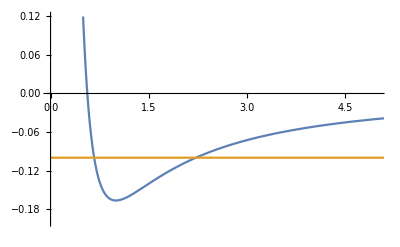

```mathematica
Plot[{Ueff[r],-0.1},{r,0,2Pi},PlotRange->{{0,5},{-.2,.12}}]
```

```mathematica
NSolve[Ueff[r]==-0.1][[2]]
```

{r→0.667079}

#### c) Write F(r) as F(u) using the substitution above and simplify

u''(ψ)=-u(ψ)-μ/(l^2(u(ψ))^2)F(u)

u''(ψ)=-u(ψ)-μ/(l^2(u(ψ))^2)(-u^(5/2)+(u(ψ))^3)

Using the assumptions μ=1,l=1

u''(ψ)=-2u(ψ)-(u(ψ))^(1/2)

To get the initial conditions we have

u=1/r and r_0=0.667079

```mathematica
Subscript[u, 0]=1/0.667079
```

1.49907

```mathematica
s=NDSolve[{y''[x]==√y[x]-y[x], y[0]==1.49907,y'[0]==0},y,{x,0,8Pi}]
```

{{y→InterpolatingFunction[{{0., 25.1327}}, <>]}}

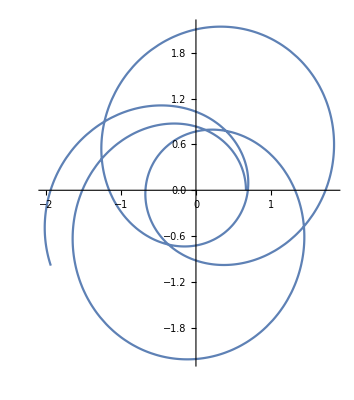

```mathematica
PolarPlot[Evaluate[1/y[x]/.s],{x,0,7.15Pi}]
```